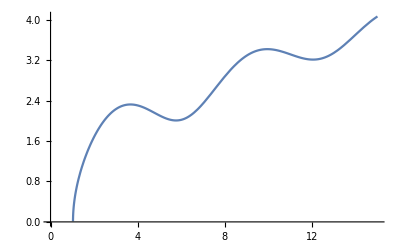

```mathematica
f[x_]:= Sqrt[x-2*Cos[x]]
Plot[f[x], {x, 0, 15}]
```

```mathematica
derf[x_]:=(1+2 Sin[x])/(2 √(x-2 Cos[x]))
```

```mathematica
der2f[x_]:=Cos[x]/(√(x-2 Cos[x]))-(1+2 Sin[x])^2/(4 (x-2 Cos[x])^(3/2))
```

```mathematica
N[f[5]]
```

2.10539

```mathematica
N[der2f[5]]
```

0.112164

```mathematica
m = FindMinimum[derf[x],{x, 1.02989, 2}][[1]]
```

-0.230984

```mathematica
c=5;
```

```mathematica
x0 = 1.02989;
```

```mathematica
x1=x0-N[f[x0]*(x0-c)/(f[x0]-f[c])]
```

1.01478

```mathematica
m*Abs[f[x1]]
```

-0.0466736

```mathematica
x2 = x1 - N[f[x1]*(x1-c)/(f[x1]-f[c])]
```

1.05115-0.378989 ⅈ

```mathematica
m*Abs[f[x2]]
```

-0.237011